```mathematica
c=3 10^8;
re=2.8179403 10^-15;
h=6.62607015 10^-34;
me=9.1093837015 10^-31;
sT=6.652 10^-29;
sK[x_]:=2 Pi re^2(((1+x)/x^2)((2+2x)/(1+2x)-Log[1+2x]/x)+Log[1+2x]/(2x)-(1+3x)/(1+2x)^2)
```

300.

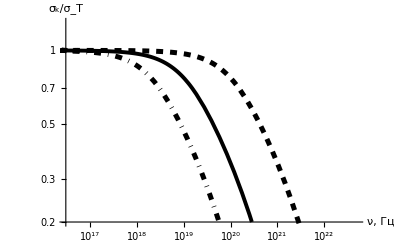

```mathematica
c/10^15*10^9//N
vel=0c;
vel1=0.8c;
vel2=0.98c;
μ=0;
Show[LogLogPlot[sK[(2h v)/(me c^2)*1/(√(1-(vel/c)^2))(1-μ vel/c)]/sT,{v,10^16,10^24},
PlotRange->{{3 10^16,5 10^22},{0.2,1.3}},PlotStyle->Directive[Black,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],
AxesLabel->{"ν, Гц","σ_k/σ_T"}],
LogLogPlot[sK[(2h v)/(me c^2)*1/(√(1-(vel2/c)^2))(1-μ vel2/c)]/sT,{v,10^16,7 10^20},
PlotRange->{{10^16,10^21},{0,1.3}},
PlotStyle->Directive[Black,DotDashed,Thickness[0.009]]],
LogLogPlot[sK[(2h v)/(me c^2)*1/(√(1-(vel2/c)^2))(1-1 vel2/c)]/sT,{v,10^16,7 10^22},
PlotRange->{{10^16,10^21},{0,1.3}},
PlotStyle->Directive[Black,Dashed,Thickness[0.009]]]
]
```

```mathematica
V1[x_,v_,ϕ_,θ_]:=x(1-v/c Cos[ϕ])/(1-v/c Cos[θ-ϕ]+(h x)/(me c^2)(1-Cos[θ])√(1-(v/c)^2))
```

```mathematica
dSk[x_,v_,ϕ_,θ_]:=re^2/2(V1[x,v,ϕ,θ]/x)^2(V1[x,v,ϕ,θ]/x+x/V1[x,v,ϕ,θ]-(Sin[θ])^2)
```

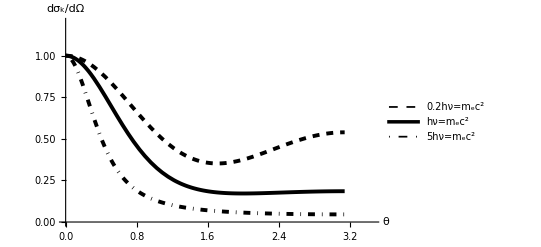

```mathematica
vv=me c^2/h;
Show[
Plot[dSk[ 0.2vv,vel,0,θ]/dSk[ 0.2vv,vel,0,0],{θ,0,Pi},
PlotRange->{{0,1.1Pi},{0,1.2}},
PlotStyle->Directive[Black,Dashed,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],
AxesLabel->{"θ","dσ_k/dΩ"},
PlotLegends->{"0.2hν=m_ec^2"}],
Plot[dSk[vv,vel,0,θ]/dSk[vv,vel,0,0],{θ,0,Pi},
PlotStyle->Directive[Black,Thickness[0.007]],
PlotLegends->{"hν=m_ec^2"}],
Plot[dSk[5vv,vel,0,θ]/dSk[5vv,vel,0,0],{θ,0,Pi},
PlotStyle->Directive[Black,DotDashed,Thickness[0.007]],
PlotLegends->{"5hν=m_ec^2"}]
]
```

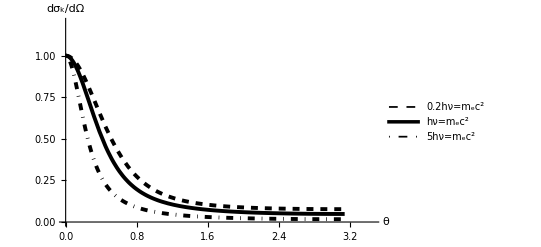

```mathematica
fi=0;
veloc=0.7 c;
Show[
Plot[dSk[ 0.2vv,veloc,fi,θ]/dSk[ 0.2vv,veloc,fi,0],{θ,0,Pi},
PlotRange->{{0,1.1Pi},{0,1.2}},
PlotStyle->Directive[Black,Dashed,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],
AxesLabel->{"θ","dσ_k/dΩ"},
PlotLegends->{"0.2hν=m_ec^2"}],
Plot[dSk[vv,veloc,fi,θ]/dSk[vv,veloc,fi,0],{θ,0,Pi},
PlotStyle->Directive[Black,Thickness[0.007]],
PlotLegends->{"hν=m_ec^2"},PlotRange->All],
Plot[dSk[5vv,veloc,fi,θ]/dSk[5vv,veloc,fi,0],{θ,0,Pi},
PlotStyle->Directive[Black,DotDashed,Thickness[0.007]],
PlotLegends->{"5hν=m_ec^2"},PlotRange->All]
]
```

```mathematica
S[ν_]:=n 1/ν^2(ν/ν1+ν1/ν+2(1/ν-1/ν1)+(1/ν-1/ν1)^2)*DiracDelta[ξ-1+1/ν1-1/ν]
```

```mathematica
(*Томсона*)
σ Integrate[3/8(1+(Cos[x])^2)Sin[x],{x,0,Pi}]
(*Реллея*)
1/(4 Pi)Integrate[3/4(1+(Cos[x])^2),{x,0,Pi}]
```

σ

9/32